# Prediction Opportunity ENSO

BX Pan
2017.10.24

## Examples

ENSO

```mathematica
impactLaNina=ImageCrop[-Graphics-];
impactElNino=ImageCrop[-Graphics-];
enso=ImageCrop[-Graphics-];
GraphicsRow[{ImageResize[enso,500],ImageResize[impactLaNina,500],ImageResize[impactElNino,500]},ImageSize->Full]
```

-Graphics-

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions

## Seeking Forecast windows ⟶ ENSO

Given that:

GCMs can capture/predict ENSO

```mathematica
nino34=-Graphics-;
nino12=-Graphics-;
nino4=-Graphics-;
nino3=-Graphics-;
GraphicsGrid[ArrayReshape[Map[ImageResize[ImageCrop[#],500]&,{nino12,nino3,nino34,nino4}],
	{2,2}],ImageSize->1200]
```

-Graphics-

It’s believed that under different phases of ENSO, precipitation for the West Coast United States would be distinct. Specifically:

```mathematica
ENSO=-Graphics-;
LANINA=-Graphics-;
GraphicsRow[Map[ImageResize[ImageCrop[#],500]&,{ENSO,LANINA}],ImageSize->Full]
```

-Graphics-

DIfference from average (1981-2010) winter precipitation (December-February) in each U.S. climate division during strong (dark gray bar), moderate (medium gray), and weak (light gray) El Niño/La Nina events since 1950. Years are ranked based on the maximum seasonal ONI index value observed. During strong El Niño events, the Gulf Coast and Southeast are consistently wetter than average. Maps by NOAA Climate.gov, based on NCDC climate division data provided by the Physical Sciences Division at NOAA ESRL.

We can deduce the following hypotheses:

GCMs can capture/predict ENSO

Implementation

DESCRIPTION: Warm (red) and cold (blue) periods based on a threshold of +/- 0.5oC for the Oceanic Niño Index (ONI) [3 month running mean of ERSST.v5 SST anomalies in the Niño 3.4 region (5oN-5oS, 120o-170oW)], based on centered 30-year base periods updated every 5 years.

```mathematica
Cluster[dataset_,threshould_:0.5]:=Block[{index,IndexTime,time,rIndex,clusters},
	index=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/ENSO/NINO34.nc",
		{"Datasets","NINO34"}];
	IndexTime=Map[DatePlus[{1960,1,1},{#,"Month"}][[1;;2]]&,Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/ENSO/NINO34.nc",
		{"Datasets","T"}]];
	time=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_control_time.mx"];
	time=Select[time,Or[#[[2]]>=10,#[[2]]≤3]&];
	rIndex=Map[index[[Position[IndexTime,#[[1;;2]]][[1,1]]]]&,time];
	clusters={Position[rIndex,_?(#>threshould&)][[;;,1]],
			  Position[rIndex,_?(#<-threshould&)][[;;,1]],
			  Position[rIndex,_?(And[#<threshould,#>-threshould]&)][[;;,1]]};
	clusters]
```

```mathematica
Evaluation[dataset_,skill_:Correlation,cluster_]:=
Block[{SCAsimu,NCAsimu,ORsimu,WAsimu,
	   SCAobser,NCAobser,ORobser,WAobser,
	   mSCAsimu,mNCAsimu,mORsimu,mWAsimu,
	   iSCAsimu,iSCAobser,iNCAsimu,iNCAobser,
	   imSCAsimu,imNCAsimu,imORsimu,imWAsimu,
	   iORsimu,iORobser,iWAsimu,iWAobser,
	   GridDaily,GridInterval,RegionalDaily,RegionalInterval,
	   int},

{{{SCAsimu,NCAsimu,ORsimu,WAsimu},{SCAobser,NCAobser,ORobser,WAobser}},
	 {{iSCAsimu,iNCAsimu,iORsimu,iWAsimu},{iSCAobser,iNCAobser,iORobser,iWAobser}}}=
	 Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_dg.mx"];
{SCAobser,NCAobser,ORobser,WAobser}=Map[#[[cluster,;;,;;]]&,{SCAobser,NCAobser,ORobser,WAobser}];	 
{SCAsimu,NCAsimu,ORsimu,WAsimu}=Map[#[[;;,cluster,;;,;;]]&,{SCAsimu,NCAsimu,ORsimu,WAsimu}];

{iSCAobser,iNCAobser,iORobser,iWAobser}=Map[Map[If[Length[#]>0,#[[cluster,;;]],#]&,#]&,{iSCAobser,iNCAobser,iORobser,iWAobser}];
{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}=Map[#[[;;,;;,cluster,;;]]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];


{mSCAsimu,mNCAsimu,mORsimu,mWAsimu}=Map[Mean,{SCAsimu,NCAsimu,ORsimu,WAsimu}];
{imSCAsimu,imNCAsimu,imORsimu,imWAsimu}=Map[Map[If[Length[#]>0,Mean[#],0]&,#]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];

	
GridDaily={Mean[Table[Table[skill[mSCAsimu[[;;,extension,grid]],SCAobser[[;;,extension,grid]]],
		{extension,Dimensions[SCAobser][[2]]}],{grid,Dimensions[SCAobser][[3]]}]],
		   Mean[Table[Table[skill[mNCAsimu[[;;,extension,grid]],NCAobser[[;;,extension,grid]]],
		{extension,Dimensions[NCAobser][[2]]}],{grid,Dimensions[NCAobser][[3]]}]],
		   Mean[Table[Table[skill[mORsimu[[;;,extension,grid]],ORobser[[;;,extension,grid]]],
		{extension,Dimensions[ORobser][[2]]}],{grid,Dimensions[ORobser][[3]]}]],
		   Mean[Table[Table[skill[mWAsimu[[;;,extension,grid]],WAobser[[;;,extension,grid]]],
		{extension,Dimensions[WAobser][[2]]}],{grid,Dimensions[WAobser][[3]]}]]};

RegionalDaily={Table[skill[Mean[Transpose[Map[Transpose,mSCAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,SCAobser]]][[;;,day]]],{day,Dimensions[SCAobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mNCAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,NCAobser]]][[;;,day]]],{day,Dimensions[NCAobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mORsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,ORobser]]][[;;,day]]],{day,Dimensions[ORobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mWAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,WAobser]]][[;;,day]]],{day,Dimensions[WAobser][[-2]]}]};
	
GridInterval={Table[If[Length[imSCAsimu[[i]]]==0,Null,
				Mean[Table[skill[imSCAsimu[[i]][[;;,grid]],iSCAobser[[i]][[;;,grid]]],{grid,Dimensions[iSCAobser[[i]]][[-1]]}]]],
				{i,Length[imSCAsimu]}],
			  Table[If[Length[imNCAsimu[[i]]]==0,Null,
				Mean[Table[skill[imNCAsimu[[i]][[;;,grid]],iNCAobser[[i]][[;;,grid]]],{grid,Dimensions[iNCAobser[[i]]][[-1]]}]]],
				{i,Length[imNCAsimu]}],
			  Table[If[Length[imORsimu[[i]]]==0,Null,
				Mean[Table[skill[imORsimu[[i]][[;;,grid]],iORobser[[i]][[;;,grid]]],{grid,Dimensions[iORobser[[i]]][[-1]]}]]],
				{i,Length[imORsimu]}],
			  Table[If[Length[imWAsimu[[i]]]==0,Null,
				Mean[Table[skill[imWAsimu[[i]][[;;,grid]],iWAobser[[i]][[;;,grid]]],{grid,Dimensions[iWAobser[[i]]][[-1]]}]]],
				{i,Length[imWAsimu]}]};

RegionalInterval={Table[If[Length[imSCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imSCAsimu[[i]]]],Mean[Transpose[iSCAobser[[i]]]]]],{i,Length[imSCAsimu]}],
				 Table[If[Length[imNCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imNCAsimu[[i]]]],Mean[Transpose[iNCAobser[[i]]]]]],{i,Length[imNCAsimu]}],
				 Table[If[Length[imNCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imORsimu[[i]]]],Mean[Transpose[iORobser[[i]]]]]],{i,Length[imORsimu]}],
				 Table[If[Length[imWAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imWAsimu[[i]]]],Mean[Transpose[iWAobser[[i]]]]]],{i,Length[imWAsimu]}]};
	
{GridDaily,RegionalDaily,GridInterval,RegionalInterval}];
```

```mathematica
models
```

{BoM,CMA,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
Visualize[dataset_]:=Block[{cluster,ElNinoBoM,LaNinaBoM,NeutralBoM,label,clusters},
label=SwatchLegend[{Blue,Red,Gray},{"El Niño","La Niña","Neutral"},
	LabelStyle->{FontSize->25},
	LegendMarkerSize->25,
	LegendLayout->"Row"];
clusters=Cluster[dataset];
ElNinoBoM=Evaluation[dataset,Correlation,clusters[[1]]];
LaNinaBoM=Evaluation[dataset,Correlation,clusters[[2]]];
NeutralBoM=Evaluation[dataset,Correlation,clusters[[3]]];
Labeled[TableForm[Table[Block[{griddaily,regionaldaily,gridinterval,regionalinterval},
griddaily=ListLinePlot[{ElNinoBoM[[1,region]],LaNinaBoM[[1,region]],NeutralBoM[[1,region]]},
	Frame->True,
	BaseStyle->15,
	ImageSize->300,
	PlotRange->Full,
	FrameLabel->{"Forecast Leading Day","Correlation"},
	PlotStyle->{Red,Blue,Gray}];
regionaldaily=ListLinePlot[{ElNinoBoM[[2,region]],LaNinaBoM[[2,region]],NeutralBoM[[2,region]]},
	Frame->True,
	BaseStyle->15,
	ImageSize->300,
	PlotRange->Full,
	FrameLabel->{"Forecast Leading Day","Correlation"},
	PlotStyle->{Red,Blue,Gray}];
gridinterval=BarChart[Transpose[{ElNinoBoM[[3,region]],
								LaNinaBoM[[3,region]],
								NeutralBoM[[3,region]]}],
	BaseStyle->10,
	BarSpacing->{0,4.},
	ChartStyle->{Red,Blue,Gray},
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	FrameLabel->{"Forecast Interval","Correlation"},
	ImageSize->300];
regionalinterval=BarChart[Transpose[{ElNinoBoM[[4,region]],
								LaNinaBoM[[4,region]],
								NeutralBoM[[4,region]]}],
	BaseStyle->10,
	BarSpacing->{0,4.},
	ChartStyle->{Red,Blue,Gray},
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	FrameLabel->{"Forecast Interval","Correlation"},
	ImageSize->300];
{griddaily,regionaldaily,gridinterval,regionalinterval}],{region,4}],
	TableSpacing->{-10,-20},
	TableHeadings->{{"SCA","NCA","OR","WA"}, {"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}},
	TableAlignments->Center
],label,Bottom]]
```

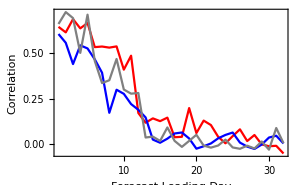
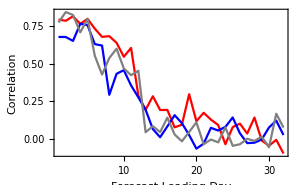
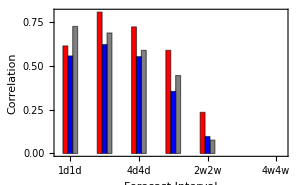
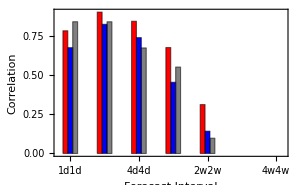
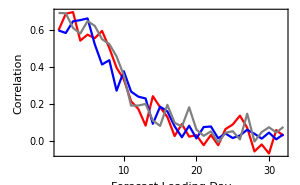
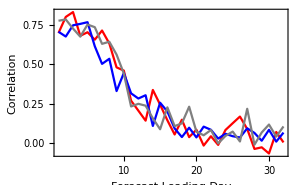
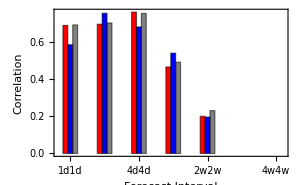
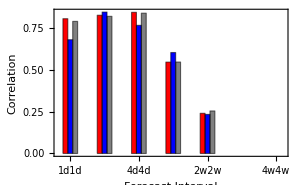
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["ECCC"]
```

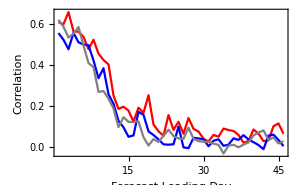
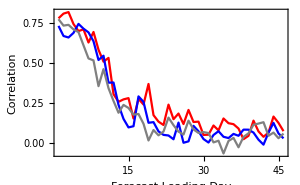
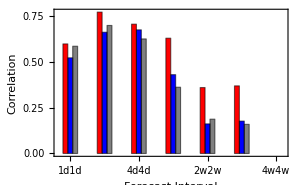
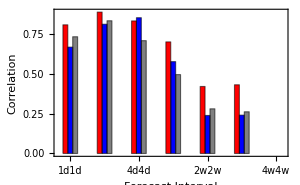
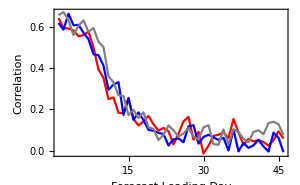
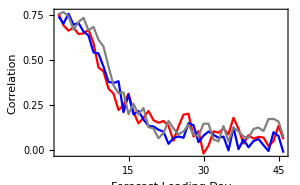
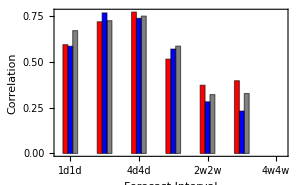
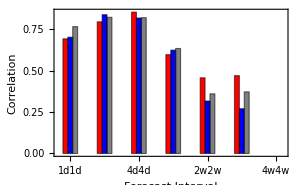
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["ECMWF"]
```

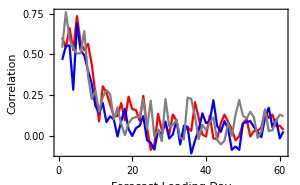
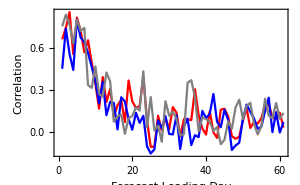
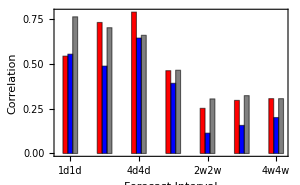
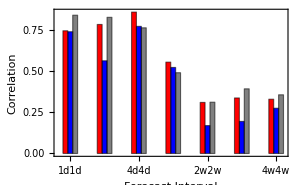
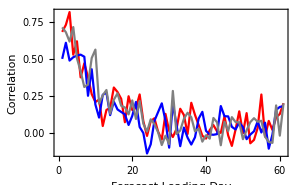
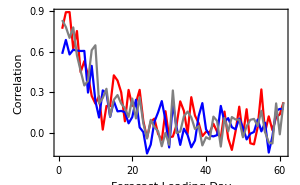
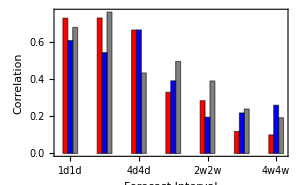
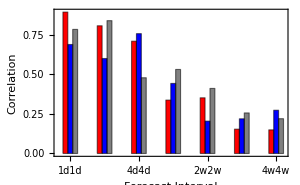
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["MeteoFrance"]
```

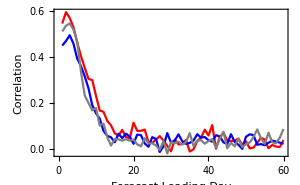
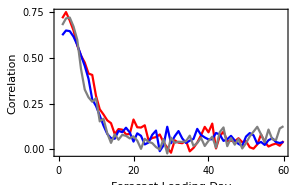
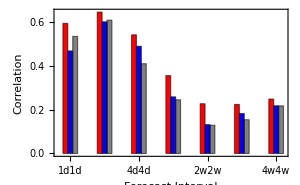
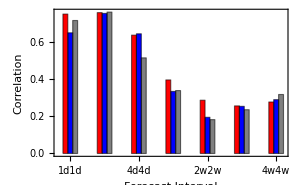
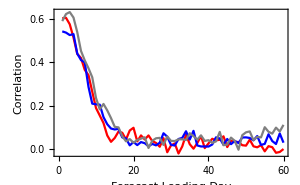
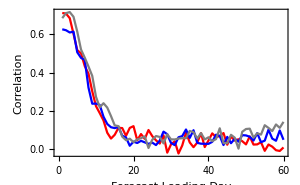
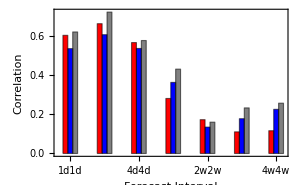
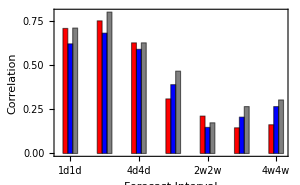
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["CMA"]
```

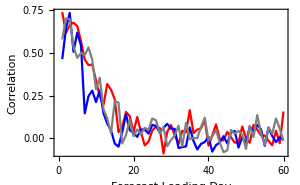
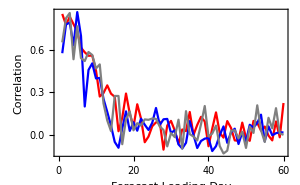
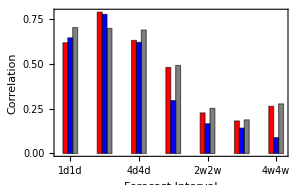
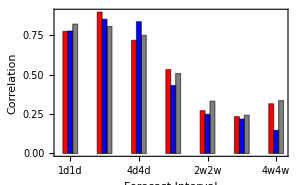
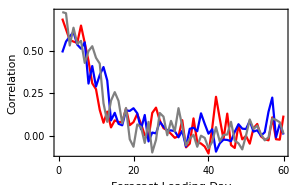
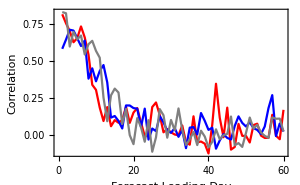
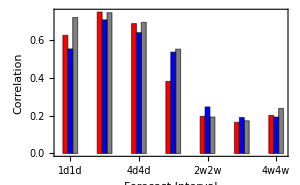
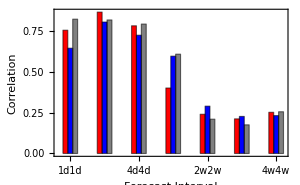
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["UKMO"]
```

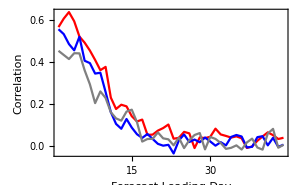
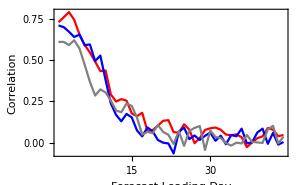
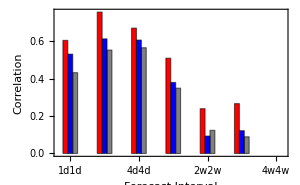
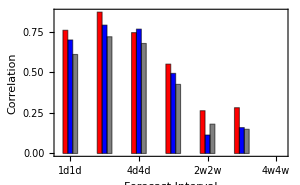
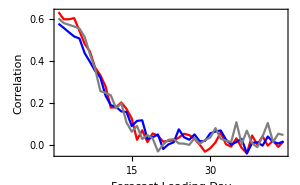
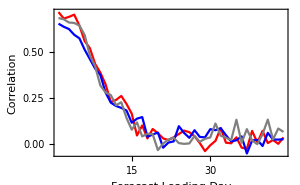
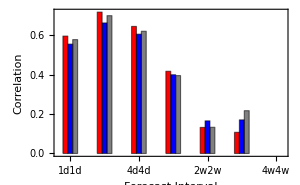
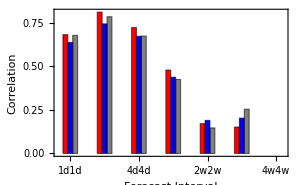
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["NCEP"]
```